## Section 1: Data Sorting

```mathematica
data = Import["/Users/ntn5160/Desktop/LF/code/20240405v020s666.txt","Table"];
```

#### ALL data

ALL  input properties

```mathematica
wai=data[[All,3]];
fai=data[[All,4]] ;(*units of 10^-17 erg/(s cm^2)*) 
lwai = data[[All,7]];
```

ALL measured properties

```mathematica
fam=data[[All,12]]; (*units of  10^-17 erg/(s cm^2)*) 
lwam=data[[All,14]];
sn=data[[All,18]];
fluxn1s=data[[All,39]];(*units of  10^-17 erg/(s cm^2)*) 
waveerr=data[[All,11]];
```

#### Survived data

Survived input properties

```mathematica
sncut = 4.8;
survivedpos=Table[fam[[k]]>0&& fluxn1s[[k]]>0&&sn[[k]]>sncut && waveerr[[k]]>0&&lwam[[k]]>0  ,{k,1,Length[data]}];
```

```mathematica
wsi = Pick[wai,survivedpos];
fsi= Pick[fai,survivedpos];
lwsi= Pick[lwai,survivedpos];
```

Survived measured properties

```mathematica
fsm =  Pick[fam,survivedpos];
sns=Pick[sn,survivedpos];
lwsm = Pick[lwam,survivedpos];
fluxn1ss=Pick[fluxn1s,survivedpos];
waveerrs=Pick[waveerr,survivedpos];
```

## Section 2: Flux to luminosity

Redshifts of input and survived wavelengths

```mathematica
lymanalphawave=1215.67;(*In ansgstrom*)
za = (wai-lymanalphawave)/lymanalphawave;
zs=(wsi-lymanalphawave)/lymanalphawave;
```

```mathematica
c=299792.458; (*km/s*)
h0=67.37;(*km/s/mpc*)
om=0.3147;
ol=1-om;
mpcInCm=3.0856776*10^24;(*cm*)
h[z_]:=h0 Sqrt[om (1+z)^3+ol];
dlIntegral[z_?NumericQ]:=(1+z)*c*NIntegrate[1/h[zp],{zp,0,z}];(*dlIntegral in mpc *)
dl=FunctionInterpolation[dlIntegral[z] mpcInCm,{z,0,5}] (*In cm*)
```

InterpolatingFunction[…]

```mathematica
Plot[dl[z]/mpcInCm,{z,0,1.4}];
```

```mathematica
lai=fai 4π dl[za]^2;(*in 10^-17 erg/s*)
laimax=Max[lai];
laimin=Min[lai];
```

```mathematica
lsi=fsi 4π dl[zs]^2;(*in 10^-17 erg/s*)
lsimax=Max[lsi];
lsimin=Max[lsi];
```

```mathematica
ListLogLinearPlot[Transpose[{lai,za}], AxesLabel->{"L (erg/s)","z"}]
```

## Section 3: Histograms and interpolating functions

```mathematica
{faiEdges,faiCounts}=HistogramList[fai,"Log"];
faiCenters=10^MovingAverage[Log10[faiEdges],2];
```

```mathematica
faiLefts = faiEdges[[1;;-2]];
faiRights =faiEdges[[2;;-1]];
```

```mathematica
faihist=Histogram[fai,{faiEdges},ScalingFunctions->{"Log","Log"},AxesLabel-> {"F (10^-17erg/(s SuperscriptBox[cm, 2]))", "Count (N)"}];
```

```mathematica
faiInterp=Interpolation[Transpose[{faiRights,faiCounts}],InterpolationOrder->0]; (*fsiInterp is the N_survived[flux]*)
faiInterpPlot= Plot[faiInterp[x],{x,Min[faiLefts],Max[faiRights]},PlotLabel->"Interpolated fai Histogram",AxesLabel->{"flux","Count"},ScalingFunctions->{"Log","Log"},PlotRange->All];
```

InterpolatingFunction::dmval: Input value {0.794418} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
faiHistListPlot= ListLogLogPlot[Transpose[{faiLefts,faiCounts} ],PlotRange->All,Joined->True,InterpolationOrder->0];
```

check(function represent data properly; histogram function is problematic when its multiplied to very small numbers)

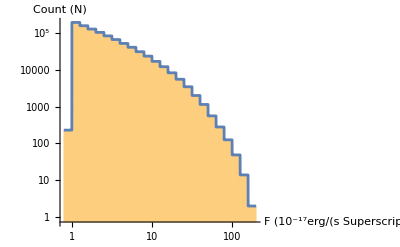

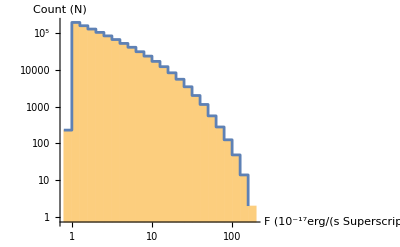

```mathematica
Show[faihist,faiInterpPlot]
Show[faihist,faiHistListPlot]
```

Lai Histogram

```mathematica
{laiEdges,laiCounts}=HistogramList[lai,"Log"];
laiCenters=10^MovingAverage[Log10[laiEdges],2];
laiLefts = laiEdges[[1;;-2]];
laiRights =laiEdges[[2;;-1]];
```

```mathematica
laihist=Histogram[lai,{laiEdges},ScalingFunctions->{"Log","Log"},AxesLabel-> {"L (10^-17erg/s)", "Count (N)"}];
```

```mathematica
laiInterp=Interpolation[Transpose[{laiRights,laiCounts}],InterpolationOrder->0]; (*fsiInterp is the N_survived[flux]*)
laiInterpPlot= Plot[laiInterp[x],{x,Min[laiLefts],Max[laiRights]},PlotLabel->"Interpolated Lai Histogram",AxesLabel->{"Luminosity","Count"},ScalingFunctions->{"Log","Log"},PlotRange->All];
```

```mathematica
laiHistListPlot= ListLogLogPlot[Transpose[{laiLefts,laiCounts} ],PlotRange->All,Joined->True,InterpolationOrder->0];
```

check

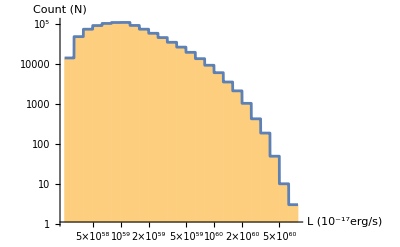

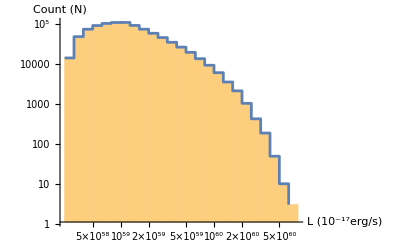

```mathematica
Show[laihist,laiInterpPlot]
Show[laihist,laiHistListPlot]
```

Fsi histogram

```mathematica
{fsiEdges,fsiCounts}=HistogramList[fsi,{faiEdges}];
fsiCenters=10^MovingAverage[Log10[fsiEdges],2];
fsiLefts = fsiEdges[[1;;-2]];
fsiRights =fsiEdges[[2;;-1]];
```

```mathematica
fsihist=Histogram[fsi,{fsiEdges},ScalingFunctions->{"Log","Log"},AxesLabel-> {"F (10^-17erg/(s SuperscriptBox[cm, 2]))", "Count (N)"}];
```

```mathematica
fsiInterp=Interpolation[Transpose[{fsiRights,fsiCounts}],InterpolationOrder->0]; (*fsiInterp is the N_survived[flux]*)
fsiInterpPlot= Plot[fsiInterp[x],{x,Min[fsiLefts],Max[fsiRights]},PlotLabel->"Interpolated fai Histogram",AxesLabel->{"flux","Count"},ScalingFunctions->{"Log","Log"},PlotRange->All];
```

InterpolatingFunction::dmval: Input value {0.794418} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.88926} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.995424} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
fsiHistListPlot= ListLogLogPlot[Transpose[{fsiLefts,fsiCounts} ],PlotRange->All,Joined->True,InterpolationOrder->0];
```

Check

```mathematica
Show[fsihist,fsiInterpPlot];
Show[fsihist,fsiHistListPlot];
```

Lsi Histogram

```mathematica
{lsiEdges,lsiCounts}=HistogramList[lsi,{laiEdges}];
lsiCenters=10^MovingAverage[Log10[lsiEdges],2];
lsiLefts = lsiEdges[[1;;-2]];
lsiRights =lsiEdges[[2;;-1]];
lsihist=Histogram[lsi,{lsiEdges},ScalingFunctions->{"Log","Log"},AxesLabel-> {"L (10^-17erg/s)", "Count (N)"}];
lsiInterp=Interpolation[Transpose[{lsiRights,lsiCounts}],InterpolationOrder->0]; (*fsiInterp is the N_survived[flux]*)
lsiInterpPlot= Plot[lsiInterp[x],{x,Min[lsiLefts],Max[lsiRights]},PlotLabel->"Interpolated Lsi Histogram",AxesLabel->{"Luminosity","Count"},ScalingFunctions->{"Log","Log"},PlotRange->All];
lsiHistListPlot= ListLogLogPlot[Transpose[{lsiLefts,lsiCounts} ],PlotRange->All,Joined->True,InterpolationOrder->0];
```

InterpolatingFunction::dmval: Input value {2.51218×10^58} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Check

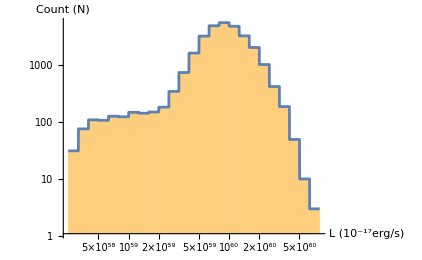

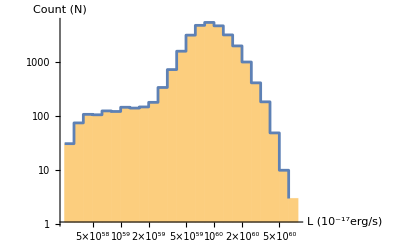

```mathematica
Show[lsihist,lsiInterpPlot]
Show[lsihist,lsiHistListPlot]
```

## Section 4: 1/V_eff

```mathematica
fcut= 1;(*in units of 10^-17 erg/s/cm^2*)
da[z_]:=dl[z]/(1+z)^2 (* in cm *)
dvdz[z_?NumericQ]:=mpcInCm  c (4 π da[z]^2)/h[z];(*in cm^3*)
condition[z_,l_]:= Boole[l> 4π dl[z]^2 fcut]
skyfrac=540/(41252.96(4.5));(*filling factor of 1/4.5*)
```

```mathematica
veffIntegral[l_?NumericQ]:=skyfrac NIntegrate[dvdz[z]condition[z,l],{z,Min[zs],Max[zs]}];
veff=FunctionInterpolation[veffIntegral[l],{l,5 10^(41+17),10^(44+17)},InterpolationOrder->1,InterpolationPoints->200];
```

```mathematica
(*in cm^3*)
```

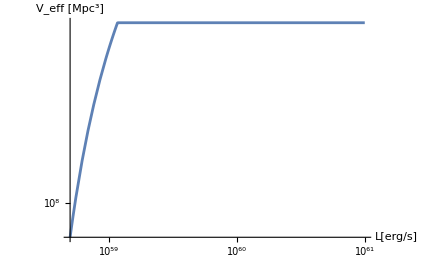

```mathematica
LogLogPlot[veff[l]/mpcInCm^3,{l,5 10^(41+17),10^(44+17)},PlotRange->All,AxesLabel->{"L[erg/s]","V_eff [Mpc^3]"}]
```

## Section 6: luminosity functions

Input LF

```mathematica
mydndlog10l[l_,a_]:= a(laiInterp[l] mpcInCm^3)/veff[l];(*Log10(10^-17 erg/s/mpc^3)*)
```

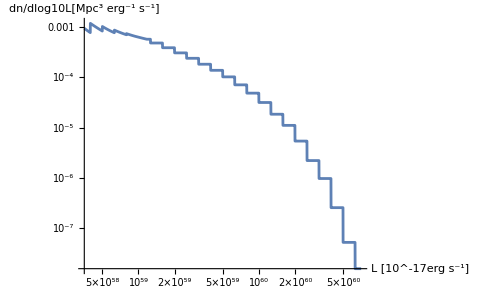

```mathematica
Plot[(laiInterp[l] mpcInCm^3)/veff[l] ,{l,Min[laiCenters[[2;;-1]]],Max[laiCenters]},AxesLabel->{"L [10^-17erg s^-1]","dn/dlog10L[Mpc^3 erg^-1 s^-1]"},ScalingFunctions->{"Log","Log"}]
```

Survived LF

```mathematica
logLFs[l_]:= (lsiInterp[l] mpcInCm^3)/veff[l];(*Log10(10^-17 erg/s/mpc^3)*)
```

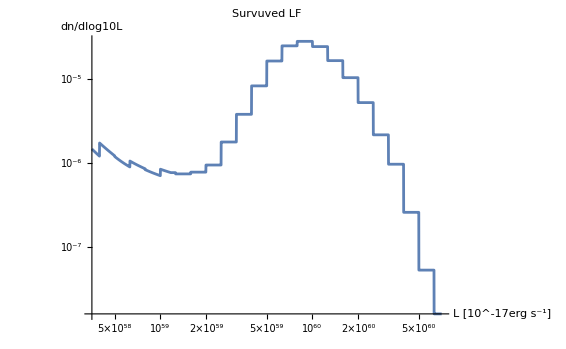

```mathematica
Plot[ logLFs[l],{l,Min[laiCenters[[2;;-1]]],Max[laiCenters]},PlotLabel->"Survuved LF",AxesLabel->{"L [10^-17erg s^-1]","dn/dlog10L"},ScalingFunctions->{"Log","Log"}]
```

## Section 5: Schechter Function

-1.8

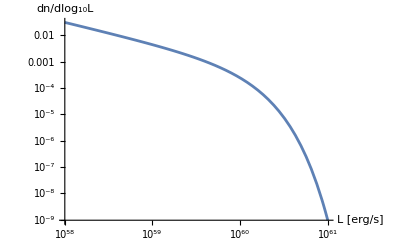

```mathematica
ϕstar=3.9*10^-4;
Lstar=0.849*10^43;
α=-1.8
fSchechter[L_,ϕstar_,Lstar_,α_]:=Module[{x},x=L/Lstar;
ϕstar*x^α*Exp[-x]];
dndlog10L[L_,ϕstar_,Lstar_,α_]:=fSchechter[L,ϕstar,Lstar,α]*(L/Lstar)*Log[10];
LFOuchi[L_]:=dndlog10L[10^-17 L,ϕstar,Lstar,α];
schechterPlot=LogLogPlot[{LFOuchi[L]},{L,10^(41+17),10^(44+17)},AxesLabel->{"L [erg/s]","dn/dlog₁₀L"},PlotRange->All]
```

## Section 6: comparison

```mathematica
binIntegrel[lmin_,lmax_]:=NIntegrate[LFOuchi[l]/(Log[10] l),{l,lmin,lmax}]
```

```mathematica
theoryhist=Table[{laiEdges[[i+1]],binIntegrel[laiEdges[[i]],laiEdges[[i+1]]]},{i,1,Length[laiEdges]-1}];
```

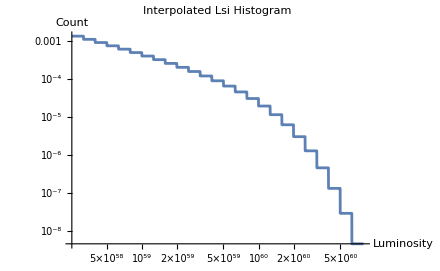

```mathematica
theoryhistInterp=Interpolation[theoryhist,InterpolationOrder->0]; 
(*fsiInterp is the N_survived[flux]*)
theoryhistInterpPlot= Plot[theoryhistInterp[x],{x,Min[lsiLefts],Max[lsiRights]},PlotLabel->"Interpolated Lsi Histogram",AxesLabel->{"Luminosity","Count"},ScalingFunctions->{"Log","Log"},PlotRange->All]
```

fit with a = 0.6 of Schechter and Input

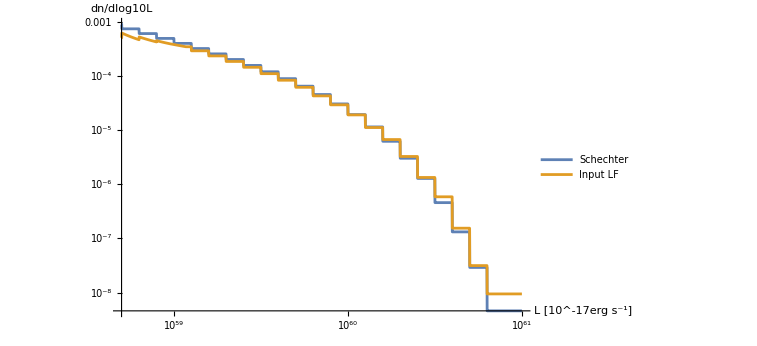

```mathematica
LogLogPlot[{theoryhistInterp[l],mydndlog10l[l,0.6] },{l,5 10^(41+17),10^(44+17)}, PlotLegends->{"Schechter", "Input LF"},AxesLabel->{"L [10^-17erg s^-1]","dn/dlog10L"}]
```

## Section5: chi square

```mathematica
chiSq[a_]:= Sum[((theoryhistInterp[l]- mydndlog10l[l,a])/(a Sqrt[laiInterp[l]] mpcInCm^3)veff[l])^2,{l,laiCenters}]
```

```mathematica
aChiSq = FindMinimum[chiSq[a],{a,0.8,0.6,1}][[2,1,2]]
```

0.895966

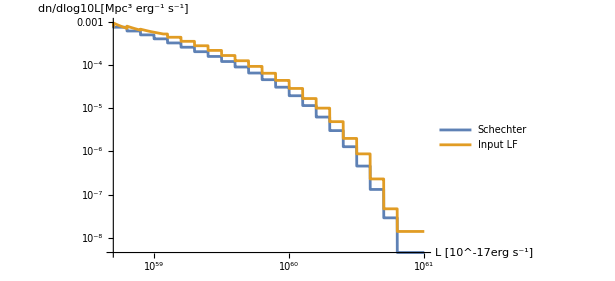

```mathematica
LogLogPlot[{theoryhistInterp[l],mydndlog10l[l,aChiSq] },{l,5 10^(41+17),10^(44+17)}, PlotLegends->{"Schechter", "Input LF"}  ,AxesLabel->{"L [10^-17erg s^-1]","dn/dlog10L[Mpc^3 erg^-1 s^-1]"}]
```

## Section 6 : F50

```mathematica
rfit[lw_,sncut_]:=Sqrt[Min[12,lw]/2.3]*(1.64-(sncut-4.8)/4.7)/(1+0.07*(12-Min[12,lw]))
lambdaVals={3499,3957,4229,4500,4771,5043,5500};
fcorVals={0.98,0.85,0.81,0.79,0.79,0.80,0.83};
fcorInterp=Interpolation[Transpose[{lambdaVals,fcorVals}],InterpolationOrder->0];
f50[fn1s_,lw_]:=fn1s*sncut*rfit[lw,sncut]*fcorInterp[wsi](*there is fn1s and fn1ss and lwai and lwsi*)
```

```mathematica
f50si= f50[fluxn1ss,lwsi ];
(*f50Edges= 10^Subdivide[Min[Log10[f50si]],Max[Log10[f50si]],4]*)
f50Edges = {Min[f50si],10,15,20,30,40,50,Max[f50si]};

f50flux= Transpose[{f50si,fsi}];
```

```mathematica
{edges,counts}= HistogramList[f50flux,{{f50Edges},{faiEdges}}];
xedges = edges[[1]];
yedges = edges[[2]];
xcenter = 10^MovingAverage[Log10[xedges],2];
ycenter = 10^MovingAverage[Log10[yedges],2];
xright = xedges[[2;;-1]];
yright = yedges[[2;;-1]];
```

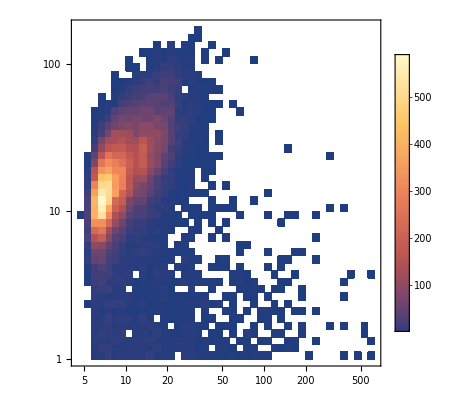

```mathematica
DensityHistogram[f50flux, {"Log",50},PlotRange->All,ChartLegends->Automatic]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {6.74775,0.891499} lies outside the range of data in the interpolating function. Extrapolation will be used.

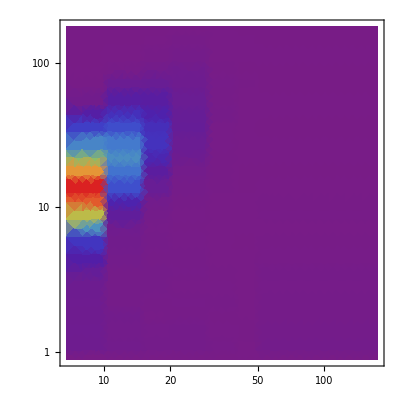

```mathematica
f50fluxdata=Reap[Do[
Sow[{{xright[[i]],yright[[j]]},counts[[i,j]]}];
,{i,1,Length[xright]},{j,1,Length[yright]}]][[2,1]];
f50fluxInterp= Interpolation[f50fluxdata,InterpolationOrder->0]
DensityPlot[f50fluxInterp[x,y],{x,Min[xcenter],Max[xcenter]},{y,Min[ycenter],Max[ycenter]},ScalingFunctions->{"Log","Log",Automatic},ColorFunction->"Rainbow",PlotRange->All,Mesh->None,PlotPoints-> 20]
```

line width

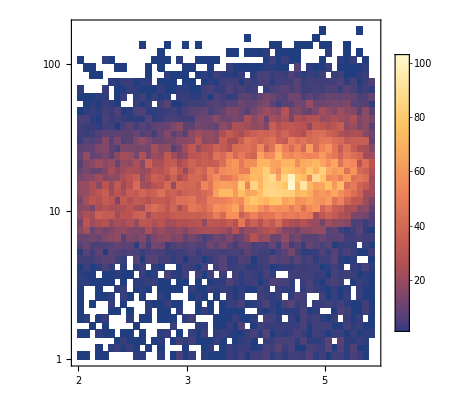

```mathematica
lwsiflux= Transpose[{lwsi,fsi}];
lwsiEdges = {Min[lwsi],3,4,Max[lwsi]};
{edges2,fluxcounts}= HistogramList[lwsiflux,{{lwsiEdges},{faiEdges}}];
xedges2 = edges2[[1]];
yedges2= edges2[[2]];
xcenter2 = 10^MovingAverage[Log10[xedges2],2];
ycenter2 = 10^MovingAverage[Log10[yedges2],2];
xright2 = xedges2[[2;;-1]];
yright2 = yedges2[[2;;-1]];
DensityHistogram[lwsiflux, {"Log",50},PlotRange->All,ChartLegends->Automatic]
```

InterpolatingFunction[…]

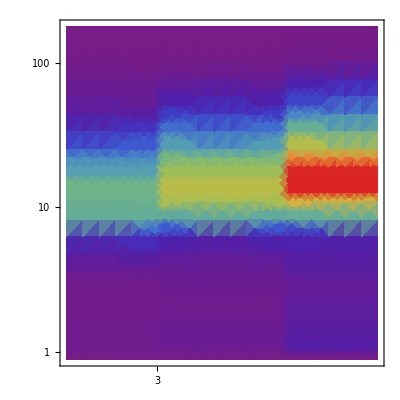

```mathematica
lwsifluxdata=Reap[Do[
Sow[{{xright2[[i]],yright2[[j]]},fluxcounts[[i,j]]}];
,{i,1,Length[xright2]},{j,1,Length[yright2]}]][[2,1]];
lwsifluxInterp= Interpolation[lwsifluxdata,InterpolationOrder->0]
DensityPlot[lwsifluxInterp[x,y],{x,Min[xcenter2],Max[xcenter2]},{y,Min[ycenter2],Max[ycenter2]},ScalingFunctions->{"Log","Log",Automatic},ColorFunction->"Rainbow",PlotRange->All,Mesh->None,PlotPoints-> 20]
```

## Section 7: completeness

```mathematica
cf[flux_]:=fsiInterp[flux]/faiInterp[flux]
```

```mathematica
cf2[f50_,flux_]:=f50fluxInterp[f50,flux]/faiInterp[flux];
```

```mathematica
cf3[lw_,flux_]:=lwsifluxInterp[lw,flux]/faiInterp[flux];
```

InterpolatingFunction::dmval: Input value {6,1.00622} lies outside the range of data in the interpolating function. Extrapolation will be used.

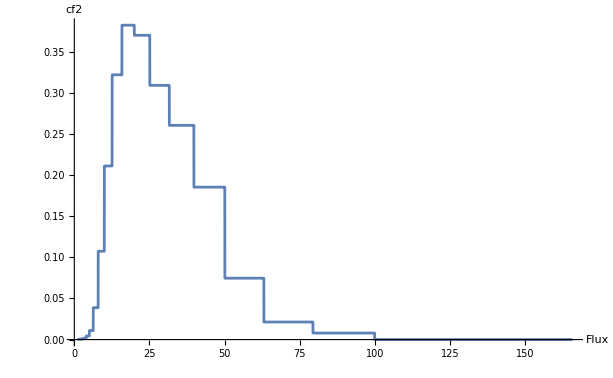

```mathematica
Plot[cf2[6,f],{f,Min[fsi],Max[fsi]},AxesLabel->{"Flux","cf2"},PlotRange->All,PlotPoints->100]
```

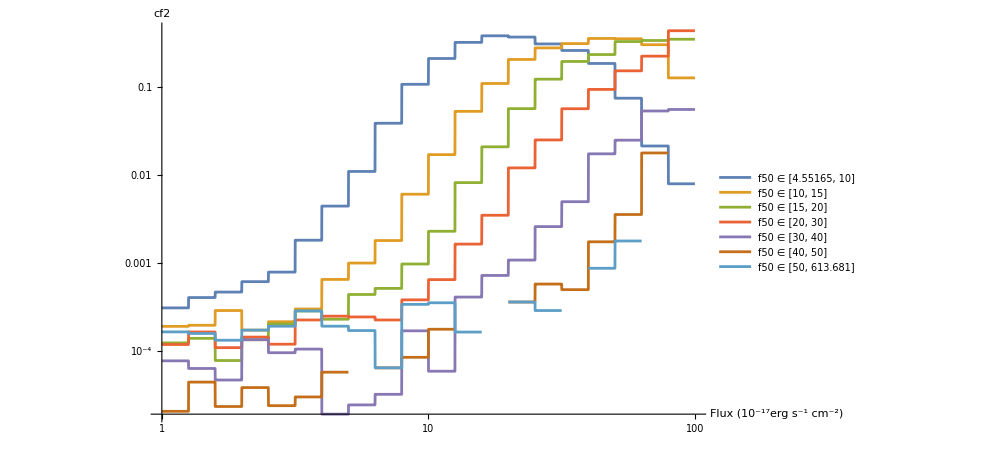

```mathematica
legends= Table["f50 ∈ ["<>ToString[xedges[[i]]]<>", "<>ToString[xedges[[i+1]]]<>"]",{i,1,Length[xedges]-1}];
LogLogPlot[Evaluate[Table[cf2[f50,f],{f50,xcenter}]],{f,0.1,100},AxesLabel->{"Flux (10^-17erg s^-1 cm^-2)","cf2"},PlotLegends->legends,PlotRange->All,PlotPoints->100]
```

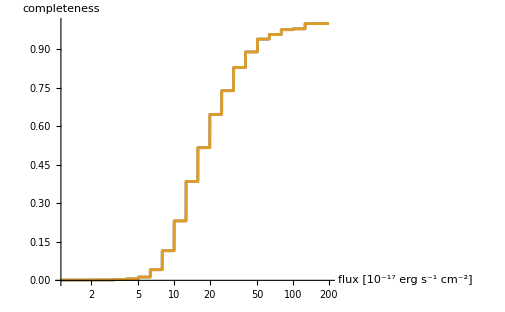

```mathematica
LogLinearPlot[{Sum[cf2[f50,x],{f50,xcenter}],cf[x]},{x,1.12,200},AxesLabel->{"flux [10^-17 erg s^-1 cm^-2]","completeness"}]
```

linewidth completeness

InterpolatingFunction::dmval: Input value {0.100007} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.44949,0.100007} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.107234} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

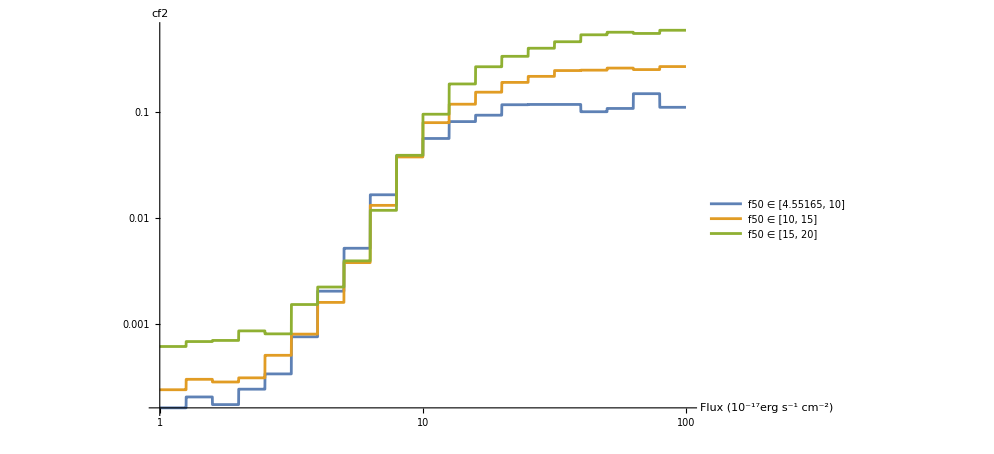

```mathematica
LogLogPlot[Evaluate[Table[cf3[lw,f],{lw,xcenter2}]],{f,0.1,100},AxesLabel->{"Flux (10^-17erg s^-1 cm^-2)","cf2"},PlotLegends->legends,PlotRange->All,PlotPoints->100]
```

```mathematica
FindRoot[cf[x]==0.5,{x,15,16}]
```

{x→15.8489}

```mathematica
cfLF[l_,z_]:= cf[l/(4 π dl[z]^2)]
```

```mathematica
trueLF[l_?NumericQ]:= (skyfrac/mpcInCm^3 NIntegrate[cfLF[l,z] dvdz[z] ,{z,Min[zs],Max[zs]} ])^-1 (*logLFs[l]*)
```

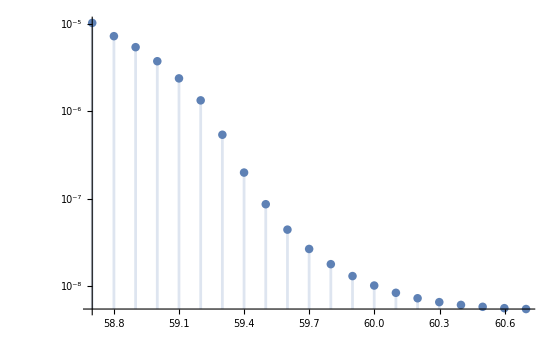

```mathematica
DiscretePlot[trueLF[10^logl],{logl,Log10[5 10^58],Log10[5 10^60],0.1},ScalingFunctions->{Automatic,"Log"}]
```

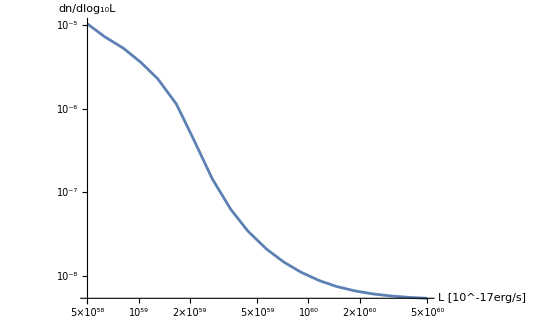

```mathematica
LogLogPlot[trueLF[l],{l,5 10^58,5 10^60},PlotPoints->20,MaxRecursion->0,AxesLabel->{"L [10^-17erg/s]","dn/dlog₁₀L"}]
```

```mathematica
DiscretePlot[trueLF[l],{l,lsiCenters}]
```

-Graphics-

```mathematica
DiscretePlot[cfLF[10^60,z] dvdz[z],{z,Min[zs],Max[zs],0.1}]
```

-Graphics-

```mathematica
cfLF[10^60,2] dvdz[2]
```

1.41138×10^84

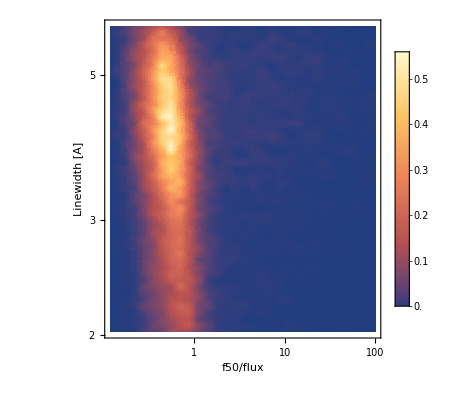

```mathematica
plot=DensityPlot[c[x,y,5 10^-17],{x,0.12,100},{y,2.02,5.95},PlotRange->All,AxesLabel->{"f50/flux","linewidth","completeness"},PlotLegends->Automatic,PlotPoints->50,ScalingFunctions->{"Log","Log"}, FrameLabel->{"f50/flux","Linewidth [A]"}]
```